```mathematica
(*Introduction*)



!X    (*Not[x]*)
x!     (*Factorial[x]*)
x+y+z     (*Plus[x,y,z]*)
{x,y,z}     (*List[x,y,z]*)
x/:y=z      (*TagSet[x,y,z]*)
OverHat[x](*Makes xhat*)
```

!X

x!

x+y+z

{x,y,z}

TagSet::tagnf: Tag x not found in y.

z

x̂

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
(*http://reference.wolfram.com/mathematica/tutorial/OperatorInputForms.html is the website to go over precedent documentation*)
```

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m;
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
{x->#^2&,(x->#^2)&,(x->#^2&)} (*Note the difference from the line of code above it, the third part requires explicit parentheses*)
```

{x→#1^2&,x→#1^2&,x→#1^2&}

```mathematica
FullForm[f^g^h^i]
```

Power[f,Power[g,Power[h,i]]]

```mathematica
$MaxNumber
```

1.23343371298165×10^323228458

```mathematica
(*What do infix, matchfix, compound, and overfix mean?*)
```

```mathematica
∫k[x] ⅆx//FullForm (*Standard Integral*)
```

Integrate[k[x],x]

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]  (*using parentheses to specify what to integrate*)
```

4[x]+∫(2[x]+3[x])ⅆx

```mathematica
x^(a+b)
```

x^5

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
(*Use parentheses to group stuff to determine the precedence of operations*)
1+2/3
(1+2)/3
```

5/3

1

```mathematica
(* the use of curley braces represents a list and is a colleciton of items referred to as the elements*)
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
{1,1,{3,4,5},{3,2}}
```

{1,3,2,3,3 x==12,√(9+y),hello}

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets are use to enclose the arguments of functions*)
Range[10]
Sin[2]
N[Sin[2]]
```

{1,2,3,4,5,6,7,8,9,10}

Sin[2]

0.909297

```mathematica
(*Double brackets are used for the Part functions to get the parts of lists*)
V=Range[10]^2
V[[3]]
```

{1,4,9,16,25,36,49,64,81,100}

9

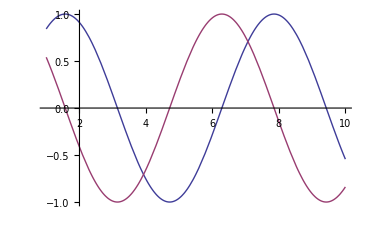

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 1, 10}]
```

```mathematica
(*Head['some expression'] gives the head of some expression*)
Head[f[j,k]]
```

f

```mathematica
Head[j+k+L]
```

Plus

```mathematica
Head[{j,k,L}]
```

List

```mathematica
Head[45]
```

Integer

```mathematica
Head[x]
```

Symbol

```mathematica
(*Things like Factor['some expression'] are commands that make something happen*)
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
(*(term) parentheses for grouping
f[x] square brackets for functions
{a,b,c} curly braces for lists
v[[i]] double brackets for indexing (Part[v,i])*)
```